```mathematica
sol=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==Exp[-x y^2],u[1,y]==(y-2)*(y-3),u[2,y]==y*(y-2)*(y-3),u[x,2]==(x-1)*(x-2),u[x,3]==x*(x-1)*(x-2)},u,{x,1,2},{y,2,3},PrecisionGoal->10]
Plot3D[sol[x,y],{x,1,2},{y,2,3}]
Table[Round[sol[x,y],.00001],{y,3,2,-.1},{x,1,2,.1}]
MatrixForm[%]
```

InterpolatingFunction[{{1., 2.}, {2., 3.}}, <>]

-Graphics3D-

{{0.,-0.099,-0.192,-0.273,-0.336,-0.375,-0.384,-0.357,-0.288,-0.171,0.},{-0.09,-0.14483,-0.20528,-0.26218,-0.30918,-0.3414,-0.35521,-0.34869,-0.32286,-0.28523,-0.261},{-0.16,-0.18609,-0.22251,-0.26147,-0.29735,-0.32648,-0.3472,-0.36061,-0.37192,-0.3933,-0.448},{-0.21,-0.21743,-0.23755,-0.26414,-0.29261,-0.32037,-0.34717,-0.37573,-0.4128,-0.47044,-0.567},{-0.24,-0.23625,-0.24642,-0.26525,-0.28897,-0.31572,-0.34602,-0.38324,-0.43419,-0.5096,-0.624},{-0.25,-0.2413,-0.24686,-0.2618,-0.28268,-0.308,-0.33853,-0.37769,-0.4318,-0.51023,-0.625},{-0.24,-0.2322,-0.23818,-0.25273,-0.27233,-0.29549,-0.32291,-0.35771,-0.40557,-0.47479,-0.576},{-0.21,-0.20949,-0.22119,-0.23893,-0.2588,-0.27912,-0.30035,-0.32511,-0.35836,-0.40763,-0.483},{-0.16,-0.17485,-0.19854,-0.22338,-0.24517,-0.26219,-0.27463,-0.28445,-0.2956,-0.31469,-0.352},{-0.09,-0.13204,-0.17529,-0.21125,-0.23659,-0.25012,-0.25186,-0.24288,-0.22551,-0.20428,-0.189},{0.,-0.09,-0.16,-0.21,-0.24,-0.25,-0.24,-0.21,-0.16,-0.09,0.}}

(0. | -0.099 | -0.192 | -0.273 | -0.336 | -0.375 | -0.384 | -0.357 | -0.288 | -0.171 | 0.
-0.09 | -0.14483 | -0.20528 | -0.26218 | -0.30918 | -0.3414 | -0.35521 | -0.34869 | -0.32286 | -0.28523 | -0.261
-0.16 | -0.18609 | -0.22251 | -0.26147 | -0.29735 | -0.32648 | -0.3472 | -0.36061 | -0.37192 | -0.3933 | -0.448
-0.21 | -0.21743 | -0.23755 | -0.26414 | -0.29261 | -0.32037 | -0.34717 | -0.37573 | -0.4128 | -0.47044 | -0.567
-0.24 | -0.23625 | -0.24642 | -0.26525 | -0.28897 | -0.31572 | -0.34602 | -0.38324 | -0.43419 | -0.5096 | -0.624
-0.25 | -0.2413 | -0.24686 | -0.2618 | -0.28268 | -0.308 | -0.33853 | -0.37769 | -0.4318 | -0.51023 | -0.625
-0.24 | -0.2322 | -0.23818 | -0.25273 | -0.27233 | -0.29549 | -0.32291 | -0.35771 | -0.40557 | -0.47479 | -0.576
-0.21 | -0.20949 | -0.22119 | -0.23893 | -0.2588 | -0.27912 | -0.30035 | -0.32511 | -0.35836 | -0.40763 | -0.483
-0.16 | -0.17485 | -0.19854 | -0.22338 | -0.24517 | -0.26219 | -0.27463 | -0.28445 | -0.2956 | -0.31469 | -0.352
-0.09 | -0.13204 | -0.17529 | -0.21125 | -0.23659 | -0.25012 | -0.25186 | -0.24288 | -0.22551 | -0.20428 | -0.189
0. | -0.09 | -0.16 | -0.21 | -0.24 | -0.25 | -0.24 | -0.21 | -0.16 | -0.09 | 0.)

InterpolatingFunction[{{0., 1.}}, <>]

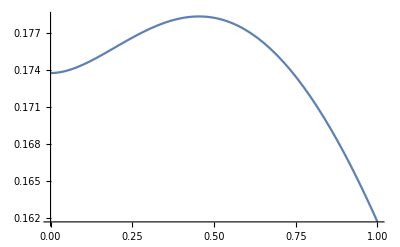

{0.17373,0.17441,0.17584,0.17727,0.17817,0.17821,0.17717,0.17498,0.17161,0.16714,0.16166}

(0.17373
0.17441
0.17584
0.17727
0.17817
0.17821
0.17717
0.17498
0.17161
0.16714
0.16166)

```mathematica
sol=NDSolveValue[{Exp[x]*u''[x] +Exp[x]*u'[x]-Exp[x]*u[x]==-Sin[x], u'[0] ==0 , -Exp[1]*u'[1]==1u[1]},u,{x, 0, 1}, PrecisionGoal->10]
Plot[sol[x],{x,0, 1}]
Table[Round[sol[x],.00001],{x,0,1,.1}]
MatrixForm[%]
```

```mathematica
sol=NDSolveValue[{D[u[x,t],t]==D[u[x,t]+x^2-2t,x,x],u[x,0]==0, (D[u[x, t],x] /.x->0)==0, u[1,t]==t},u,{x,0,1},{t,0,1},PrecisionGoal->10]
Plot3D[sol[x,t],{x,0,1},{t,0,1}]
Table[Round[sol[x,t],.00001],{t,0,1,.1},{x,0,1,.1}]
MatrixForm[%]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

-Graphics3D-

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.19882,0.19856,0.19773,0.19608,0.19321,0.18851,0.18113,0.17001,0.15381,0.13103,0.1},{0.38524,0.38409,0.38055,0.37436,0.36506,0.35206,0.33459,0.31172,0.28244,0.2456,0.2},{0.55389,0.55191,0.54592,0.53569,0.52085,0.50092,0.47529,0.44322,0.40391,0.35648,0.3},{0.70766,0.70502,0.69706,0.68361,0.66438,0.63897,0.60692,0.56766,0.52055,0.4649,0.4},{0.84967,0.84652,0.83703,0.82105,0.79838,0.7687,0.73163,0.68675,0.63354,0.57148,0.5},{0.98251,0.97896,0.96826,0.95032,0.92495,0.89192,0.85094,0.80166,0.74369,0.67662,0.6},{1.10821,1.10434,1.09271,1.07322,1.04575,1.0101,0.96606,0.91334,0.85164,0.78064,0.7},{1.22831,1.2242,1.21183,1.19113,1.16201,1.12432,1.07787,1.02246,0.95785,0.88379,0.8},{1.34401,1.3397,1.32675,1.30512,1.27471,1.23541,1.18709,1.12959,1.0627,0.98624,0.9},{1.45626,1.45179,1.4384,1.41602,1.38461,1.34407,1.29429,1.23514,1.16648,1.08816,1.}}

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.19882 | 0.19856 | 0.19773 | 0.19608 | 0.19321 | 0.18851 | 0.18113 | 0.17001 | 0.15381 | 0.13103 | 0.1
0.38524 | 0.38409 | 0.38055 | 0.37436 | 0.36506 | 0.35206 | 0.33459 | 0.31172 | 0.28244 | 0.2456 | 0.2
0.55389 | 0.55191 | 0.54592 | 0.53569 | 0.52085 | 0.50092 | 0.47529 | 0.44322 | 0.40391 | 0.35648 | 0.3
0.70766 | 0.70502 | 0.69706 | 0.68361 | 0.66438 | 0.63897 | 0.60692 | 0.56766 | 0.52055 | 0.4649 | 0.4
0.84967 | 0.84652 | 0.83703 | 0.82105 | 0.79838 | 0.7687 | 0.73163 | 0.68675 | 0.63354 | 0.57148 | 0.5
0.98251 | 0.97896 | 0.96826 | 0.95032 | 0.92495 | 0.89192 | 0.85094 | 0.80166 | 0.74369 | 0.67662 | 0.6
1.10821 | 1.10434 | 1.09271 | 1.07322 | 1.04575 | 1.0101 | 0.96606 | 0.91334 | 0.85164 | 0.78064 | 0.7
1.22831 | 1.2242 | 1.21183 | 1.19113 | 1.16201 | 1.12432 | 1.07787 | 1.02246 | 0.95785 | 0.88379 | 0.8
1.34401 | 1.3397 | 1.32675 | 1.30512 | 1.27471 | 1.23541 | 1.18709 | 1.12959 | 1.0627 | 0.98624 | 0.9
1.45626 | 1.45179 | 1.4384 | 1.41602 | 1.38461 | 1.34407 | 1.29429 | 1.23514 | 1.16648 | 1.08816 | 1.)